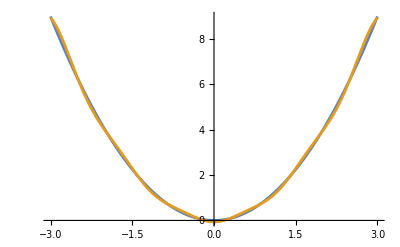

```mathematica
f=FourierSeries[x^2,x,5];
Plot[{x^2,f},{x,-3,3}]
```

```mathematica
ClearAll[v]
v[x_]:=Piecewise[{{-3,Abs[x]<=1},{0,True}}]
```

```mathematica
p=Range[-10,10,3]
```

{-10,-7,-4,-1,2,5,8}

```mathematica
V=Sum[v[x-pp],{pp,p}]
```

(Piecewise[{{-3, Abs[-8+x]≤1}, {0, True}}])+(Piecewise[{{-3, Abs[-5+x]≤1}, {0, True}}])+(Piecewise[{{-3, Abs[-2+x]≤1}, {0, True}}])+(Piecewise[{{-3, Abs[1+x]≤1}, {0, True}}])+(Piecewise[{{-3, Abs[4+x]≤1}, {0, True}}])+(Piecewise[{{-3, Abs[7+x]≤1}, {0, True}}])+(Piecewise[{{-3, Abs[10+x]≤1}, {0, True}}])

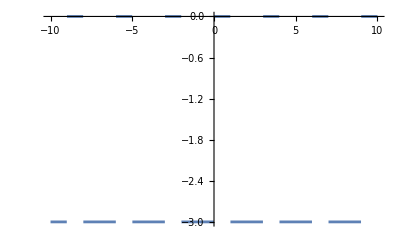

```mathematica
Plot[V,{x,-10,10}]
```

```mathematica
FourierCoefficient[V,x,n]//FullSimplify
```

Piecewise[{{-(3 (1+π))/(2 π), n==0}, {(ⅇ^(-2 ⅈ n) (-3 ⅈ (ⅇ^(5 ⅈ n)-ⅇ^(ⅈ n (2+π)))-6 (1+ⅇ^(3 ⅈ n)) Sin[n]))/(2 n π), True}}]

```mathematica
f=FourierSeries[V,x,5]
```

(3 ⅈ (1-ⅇ^ⅈ+2 ⅇ^(3 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(6 ⅈ)) ⅇ^(-3 ⅈ-ⅈ x))/(2 π)-(3 ⅈ (1-ⅇ^(4 ⅈ)-ⅇ^(10 ⅈ)+ⅇ^(12 ⅈ)) ⅇ^(-6 ⅈ+2 ⅈ x))/(4 π)+(ⅈ (1-ⅇ^(3 ⅈ)+2 ⅇ^(9 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(18 ⅈ)) ⅇ^(-9 ⅈ-3 ⅈ x))/(2 π)+(3 ⅈ (1-ⅇ^(4 ⅈ)-ⅇ^(16 ⅈ)+ⅇ^(24 ⅈ)) ⅇ^(-12 ⅈ-4 ⅈ x))/(8 π)-(3 (1+π))/(2 π)-(3 ⅈ ⅇ^(-2 ⅈ+ⅈ x) (2 ⅇ^(2 ⅈ)-ⅇ^(4 ⅈ)+ⅇ^(5 ⅈ)-2 ⅈ Sin[1]))/(2 π)-(3 ⅇ^(-3 ⅈ-2 ⅈ x) (ⅇ^ⅈ Sin[2]+ⅇ^(7 ⅈ) Sin[2]-Sin[3]))/(2 π)-(ⅈ ⅇ^(-6 ⅈ+3 ⅈ x) (2 ⅇ^(6 ⅈ)-ⅇ^(12 ⅈ)+ⅇ^(15 ⅈ)-2 ⅈ Sin[3]))/(2 π)-(3 ⅈ ⅇ^(-8 ⅈ+4 ⅈ x) (-ⅇ^(16 ⅈ)+ⅇ^(20 ⅈ)-2 ⅈ Sin[4]))/(8 π)-(3 ⅈ ⅇ^(-10 ⅈ+5 ⅈ x) (2 ⅇ^(10 ⅈ)-ⅇ^(20 ⅈ)+ⅇ^(25 ⅈ)-2 ⅈ Sin[5]))/(10 π)-(3 (1+ⅇ^(15 ⅈ)) ⅇ^(-15 ⅈ-5 ⅈ x) (-ⅈ+2 ⅇ^(10 ⅈ) Sin[5]))/(10 π)

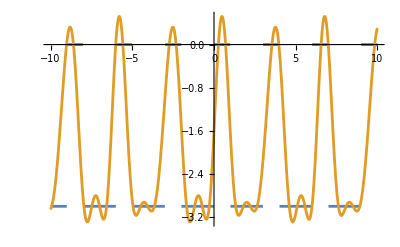

```mathematica
Plot[{V,f},{x,-10,10}]
```

```mathematica
InverseFourierTransform[V,x,ω]//Simplify
```

-(3 ⅇ^(-8 ⅈ ω) √(2/π) (1+2 Cos[3 ω]+2 Cos[6 ω]+2 Cos[9 ω]) Sin[ω] (Cos[9 ω]+ⅈ Sin[9 ω]))/ω

```mathematica
Integrate[Exp[-I ]]
```

```mathematica
a=ResourceFunction["RandomMatrix"][Reals,{0,1},{3,3}]
```

```mathematica
a
```

```mathematica
a=ResourceFunction["RandomMatrix"][Real,{0,1},12];
Eigenvalues[a]
```

{6.22059+0. ⅈ,0.0268122+1.06379 ⅈ,0.0268122-1.06379 ⅈ,0.799482+0. ⅈ,-0.747859+0.135188 ⅈ,-0.747859-0.135188 ⅈ,0.551921+0.335164 ⅈ,0.551921-0.335164 ⅈ,-0.235041+0.476307 ⅈ,-0.235041-0.476307 ⅈ,0.107034+0.202874 ⅈ,0.107034-0.202874 ⅈ}

```mathematica
DiagonalMatrix[Range[1.,4]]
```

{{1.,0.,0.,0.},{0.,2.,0.,0.},{0.,0.,3.,0.},{0.,0.,0.,4.}}

```mathematica
Eigenvalues[%]
```

{4.,3.,2.,1.}